```mathematica
(*Quit[]*)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/luchinsky/Dropbox/DskD/Work/bc/bc_chi_npi/Math

# B_c(p1)→χ_cJ(p2, {α,β}) + W_μ(q)

```mathematica
(*Ebert, Faustov, Galkin, arXiv:1007.1369 [hep-ph]*)
```

## Init

```mathematica
<<FeynCalc`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or write to the mailing list.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, P3H-20-002, TTP19-020, TUM-EFT 130/19, arXiv:2001.04407

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

```mathematica
<<MyPackages`ChDim`
```

```mathematica
ClearScalarProducts[];
ScalarProduct[p1, p1]=MBc^2; ScalarProduct[p2, p2]=Mcc^2; ScalarProduct[q,q]=q2;
ScalarProduct[p1,p2]=Calc[(SP[p1]+SP[p2]-SP[q])/2];
ScalarProduct[p1, q]=Calc[(SP[p1]+SP[q]-SP[p2])/2];
ScalarProduct[p2,q]=Calc[(SP[p1]-SP[p2]-SP[q])/2];
Calc[SP[#]&/@{p2+q, p1-q, p1-p2}]
```

{MBc^2,Mcc^2,q2}

```mathematica
SetOptions[ChDim, Dimensions->{
GF->-2,
a1->0, beta->0, Vbc->0, Vuq->0,
mu->0,a->0, b->0,
rhoL[_]->0, rhoT[_]->0,
fPlus[_]->0, fMinus[_]->0,
hA[_]->0, hV1[_]->0, hV2[_]->0, hV3[_]->0,
tV[_]->0, tA1[_]->0, tA2[_]->0, tA3[_]->0,
fP->1, mP->1, fV->1, mV->1,
p1->1, p2->1,q->1, MBc->1, Mcc->1,
q2->2}];
```

```mathematica
chiList = {"chi_c0", "chi_c1", "chi_c2"};
```

```mathematica
<<"./mdat/amps.mdat";
```

```mathematica
<<"./mdat/ebert_ff.mdat";
```

## Numbers

```mathematica
gammaTot = (6.6*10^-22 10^-3)/(0.5*10^-12);
```

```mathematica
Clear[getMcc];
(* 1P masses from PDG *)
getMcc[out_, type_:"1P"]:=Switch[out,"chi_c0", 3414.71MeV,"chi_c1", 3510.67MeV,"chi_c2", 3556.17MeV]
(* 2P masses are chosen to fit Ebert's distributions *)
getMcc[out_, "2P"]:=Switch[out,"chi_c0", 3862MeV,"chi_c1", 3.9214,"chi_c2",3.967735]
```

```mathematica
GeV=1.; MeV=10^-3 GeV;
```

```mathematica
$MBc = 6274.47MeV;
$mPi = 0.140GeV;
$a1 = 1.14;
Clear[Ngamma];
Ngamma[out_, outL_, type_:"1P"]:=Module[{
$Mcc=getMcc[out, type],
$q2=Switch[outL,"P", mPi, "V", mV, "W",q2],
fffit = Switch[type,"1P",ffFitRule,"2P", ffFitRule$2P]
},
gamma[out, outL]//.{
beta -> √(1-((Mcc+√q2)/MBc)^2)√(1-((Mcc-√q2)/MBc)^2),
GF->1.16*10^-5 GeV^-2,fP->130MeV,fV->208MeV,
Vuq ->0.973,Vbc-> 40.8*10^-3,a1 ->$a1
}//.{MBc -> $MBc, mPi->$mPi, mV->775MeV, Mcc->$Mcc, q2->$q2}/.fffit]
Ngamma[out_, "enu",type_:"1P"]:=Ngamma[out,"W", type]/.{rhoL[_]->0, rhoT[_]->1/(6 π^2)}
```

```mathematica
Clear[q2Max];
q2Max[out_,type_:"1P"]:=($MBc-getMcc[out,type])^2;
```

### Two-Body Decays

```mathematica
Clear[$gamma];
$gamma::usage="$gamma[out, outL, type] is the width of Bc -> out outL decay from tables II, VI (in 10^-15GeV)";
$gamma[out_,outL_]:=$gamma[out,outL,"1P"];
(* Table VI *)
$gamma["chi_c0","P","1P"] = 0.23($a1)^2;
$gamma["chi_c0","V","1P"] = 0.64($a1)^2;
$gamma["chi_c1","P","1P"] = 0.22($a1)^2;
$gamma["chi_c1","V","1P"] = 0.16($a1)^2;
$gamma["chi_c2","P","1P"] = 0.41($a1)^2;
$gamma["chi_c2","V","1P"] = 1.18($a1)^2;
(**)
$gamma["chi_c0","P","2P"] = 0.023($a1)^2;
$gamma["chi_c0","V","2P"] = 0.080($a1)^2;
$gamma["chi_c1","P","2P"] = 0.011($a1)^2;
$gamma["chi_c1","V","2P"] = 0.016($a1)^2;
$gamma["chi_c2","P","2P"] = 8.5*10^-7($a1)^2;
$gamma["chi_c2","V","2P"] = 0.0022($a1)^2;
```

```mathematica
outL="P"; type="1P";
Do[
Print["Bc ->"<> out<>"("<>type<>") "<>outL<>":\t this/Ebert=", 10^15 Ngamma[out, outL, type]/$gamma[out,outL, type]
]
,{out, chiList}]
```

Bc ->chi_c0(1P) P:	 this/Ebert=0.987324

Bc ->chi_c1(1P) P:	 this/Ebert=0.0582581

Bc ->chi_c2(1P) P:	 this/Ebert=0.958299

```mathematica
outL="V"; type="1P";
Do[
Print["Bc ->"<> out<>"("<>type<>") "<>outL<>":\t this/Ebert=", 10^15 Ngamma[out, outL, type]/$gamma[out,outL, type]
]
,{out, chiList}]
```

Bc ->chi_c0(1P) V:	 this/Ebert=0.703591

Bc ->chi_c1(1P) V:	 this/Ebert=0.865832

Bc ->chi_c2(1P) V:	 this/Ebert=0.694878

```mathematica
outL="P"; type="2P";
Do[
Print["Bc ->"<> out<>"("<>type<>") "<>outL<>":\t this/Ebert=", 10^15 Ngamma[out, outL, type]/$gamma[out,outL, type]
]
,{out, chiList}]
```

Bc ->chi_c0(2P) P:	 this/Ebert=1.0626

Bc ->chi_c1(2P) P:	 this/Ebert=0.378969

Bc ->chi_c2(2P) P:	 this/Ebert=39.3025

```mathematica
outL="V"; type="2P";
Do[
Print["Bc ->"<> out<>"("<>type<>") "<>outL<>":\t this/Ebert=", 10^15 Ngamma[out, outL, type]/$gamma[out,outL, type]
]
,{out, chiList}]
```

Bc ->chi_c0(2P) V:	 this/Ebert=0.784713

Bc ->chi_c1(2P) V:	 this/Ebert=0.840521

Bc ->chi_c2(2P) V:	 this/Ebert=1.16257

### Semileptonic decays

```mathematica
Clear[extractFF];
extractFF::usage="extractFF[json, num]";
extractFF[json_, n_, fact_:1]:=Module[{name, data},
name = json⟦3,2,n,1,2⟧;
data = json⟦3,2,n,5,2,All,3,2⟧;
data⟦All,2⟧=fact*data⟦All,2⟧;
Return[<|"name"->name,"data"->data|>]
]
```

```mathematica
distEE["chi_c0"] = extractFF[Import["../literatute/Ebert_FFs/fig4_chic0_1P.json"], 1]["data"];
distEE["chi_c1"] = extractFF[Import["../literatute/Ebert_FFs/fig4_chic1_1P.json"], 1]["data"];
distEE["chi_c2"] = extractFF[Import["../literatute/Ebert_FFs/fig4_chic2_1P.json"], 1]["data"];
```

```mathematica
distEE["chi_c0","2P"] = extractFF[Import["../literatute/Ebert_FFs/fig4_chic0_2P.json"], 1]["data"];
distEE["chi_c1","2P"] = extractFF[Import["../literatute/Ebert_FFs/fig4_chic1_2P.json"], 1]["data"];
distEE["chi_c2","2P"] = extractFF[Import["../literatute/Ebert_FFs/fig4_chic2_2P.json"], 1]["data"];
```

```mathematica
out = "chi_c0";
root=ReadList["../c++/build/"<>out<>"_en.txt", {Number,Number,Number}];
root⟦All,2;;3⟧*=Max[distEE[out]⟦All,2⟧]/Max[root⟦All,2⟧];
Show[
ListPlot[distEE[out], PlotStyle->Red],
Plot[0.8 10^13/(40.8*10^-3)^2 Ngamma[out,"enu"], {q2, 0.2,8}],
ListPlot[root⟦All,1;;2⟧, PlotMarkers->"o"]
, AxesLabel->{"q2, GeV^2", "ⅆΓ/ⅆq2(|V_cb|^210^-13)"}, PlotLabel->out]
Print["Br[Ebert]/Br[this]=",1.27/(10^15 NIntegrate[Ngamma[out,"enu"],{q2,0,q2Max[out]}])]
```

-Graphics-

Br[Ebert]/Br[this]=0.809794

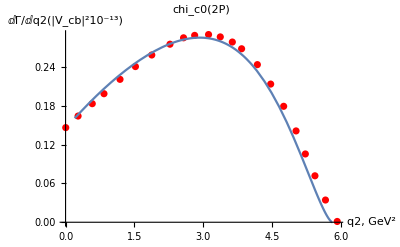

Br[Ebert]/Br[this]=0.766061

```mathematica
out = "chi_c0";
Show[
ListPlot[distEE[out,"2P"], PlotStyle->Red],
Plot[0.82 10^13/(40.8*10^-3)^2 Ngamma[out,"enu","2P"], {q2, 0.2,8}],
AxesLabel->{"q2, GeV^2", "ⅆΓ/ⅆq2(|V_cb|^210^-13)"}, PlotLabel->out<>"(2P)"]
Print["Br[Ebert]/Br[this]=",0.19/(10^15 NIntegrate[Ngamma[out,"enu", "2P"],{q2,0,q2Max[out, "2P"]}])]
```

```mathematica
out = "chi_c1";
root=ReadList["../c++/build/"<>out<>"_en.txt", {Number,Number,Number}];
root⟦All,2;;3⟧*=Max[distEE[out]⟦All,2⟧]/Max[root⟦All,2⟧];
Show[
ListPlot[distEE[out], PlotStyle->Red],
Plot[0.84 10^13/(40.8*10^-3)^2 Ngamma[out,"enu"], {q2, 0.2,8}],
ListPlot[root⟦All,1;;2⟧, PlotMarkers->"o"]
, AxesLabel->{"q2, GeV^2", "ⅆΓ/ⅆq2(|V_cb|^210^-13)"}, PlotLabel->out]
Print["Br[Ebert]/Br[this]=",1.18/(10^15 NIntegrate[Ngamma[out,"enu"],{q2,0,q2Max[out]}])]
```

-Graphics-

Br[Ebert]/Br[this]=0.833344

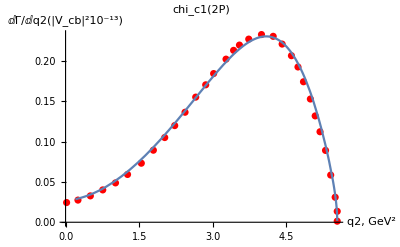

Br[Ebert]/Br[this]=0.790591

```mathematica
out = "chi_c1";
Show[
ListPlot[distEE[out,"2P"], PlotStyle->Red],
Plot[0.8 10^13/(40.8*10^-3)^2 Ngamma[out,"enu","2P"], {q2, 0.2,8}],
 AxesLabel->{"q2, GeV^2", "ⅆΓ/ⅆq2(|V_cb|^210^-13)"}, PlotLabel->out<>"(2P)"]
Print["Br[Ebert]/Br[this]=",0.12/(10^15 NIntegrate[Ngamma[out,"enu", "2P"],{q2,0,q2Max[out,"2P"]}])]
```

```mathematica
out = "chi_c2";
root=ReadList["../c++/build/"<>out<>"_en.txt", {Number,Number,Number}];
root⟦All,2;;3⟧*=Max[distEE[out]⟦All,2⟧]/Max[root⟦All,2⟧];
Show[
ListPlot[distEE[out], PlotStyle->Red],
Plot[0.82 10^13/(40.8*10^-3)^2 Ngamma[out,"enu"], {q2, 0.2,8}],
ListPlot[root⟦All,1;;2⟧, PlotMarkers->"o"]
, AxesLabel->{"q2, GeV^2", "ⅆΓ/ⅆq2(|V_cb|^210^-13)"}, PlotLabel->out]
Print["Br[Ebert]/Br[this]=",2.27/(10^15 NIntegrate[Ngamma[out,"enu"],{q2,0,q2Max[out]}])]
```

-Graphics-

Br[Ebert]/Br[this]=0.828582

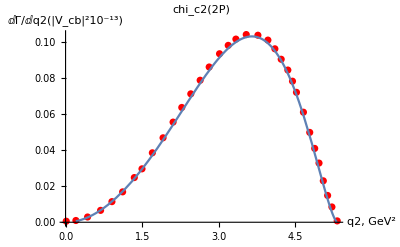

Br[Ebert]/Br[this]=0.872035

```mathematica
out = "chi_c2";
Show[
ListPlot[distEE[out,"2P"], PlotStyle->Red],
Plot[0.84 10^13/(40.8*10^-3)^2 Ngamma[out,"enu","2P"], {q2, 0.2,8}]
, AxesLabel->{"q2, GeV^2", "ⅆΓ/ⅆq2(|V_cb|^210^-13)"}, PlotLabel->out<>"(2P)"]
Print["Br[Ebert]/Br[this]=",0.048/(10^15 NIntegrate[Ngamma[out,"enu","2P"],{q2,0,q2Max[out,"2P"]}])]
```

### nπ decays

### Spectral functions and constants

```mathematica
(* See file Dropbox/Dsk/Baryons/OmegaQQ_NPi/February_final.nb for detailed calulations *)
Fq2π=(0.0013516183448589506*(1+0.6384423540947195*q2)*(-0.07840000000000001+q2)^2)/((0.013064170424296547+(-0.5686550420645691+q2)^2)*q2^2);
Const2π=1.2559939710150794;
Fq3π=(0.000058592966004157997*(-0.17640000000000003+q2)^4*(1+1.510651725804281*^-105*q2+189.45911486214024*q2^2))/((0.48273650253772327+(-1.0373349238887504+q2)^2)^2*q2^4)/2;
Const3π =1.3415359909807425;
Fq4π=(0.00017983715820604627*(-0.31360000000000005+q2)*(1+5.074780646730226*q2+8.631754238222705*q2^2))/((0.6162735882355033+(-1.834698151162789+q2)^2)^2*q2);
Const4π=1.2343872367174031;
Fq5π=32*((q2-25*mπ^2)/q2)^10*(1-1.65*q2+0.69q2^2)/(((q2+2.21)^2-4.69)^3);
Const5π=0.8420445176523225;
```

```mathematica
<<MyPackages`HistV2`
```

```mathematica
Clear[readROOT];
Options[readROOT]={Norm->False, Color->Red};
readROOT[fileName_,OptionsPattern[]]:=Module[{root},
root = ReadList[fileName,{Number,Number,Number}];
root = HST2D[{#⟦1⟧,#⟦2⟧±#⟦3⟧}&/@root, PlotStyle->OptionValue[Color]];
If[!OptionValue[Norm]=!=False,
root *= OptionValue[Norm]/IntegralHST[root];
];
root
]
```

### chi_c0

```mathematica
out="chi_c0"
```

chi_c0

```mathematica
Clear[brNPI];
brNPI::usage="brNPI[out, n]";
```

Br(2π)=0.0597652 %

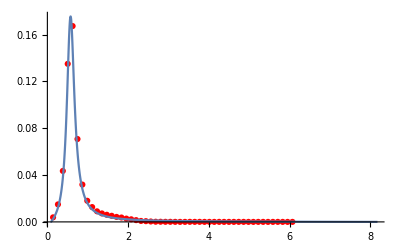

```mathematica
br = NIntegrate[100/gammaTot Ngamma[out,"W"]/.{rhoL[_]->0,rhoT[_]->Const2π*Fq2π},{q2, (2*$mPi)^2,q2Max[out]}];
brNPI[out, 2]=br;
Print["Br(2π)=",br," %"];
root = readROOT["../c++/results/"<>out<>"_2pi_q2.txt",Norm->br];
Show[
PlotHST[1.1root],
Plot[100/gammaTot Ngamma[out,"W"]/.{rhoL[_]->0,rhoT[_]->Const2π*Fq2π},{q2, (2*$mPi)^2,q2Max[out]}, PlotRange->All]
,PlotRange->All]
```

Br(3π)=0.0371442 %

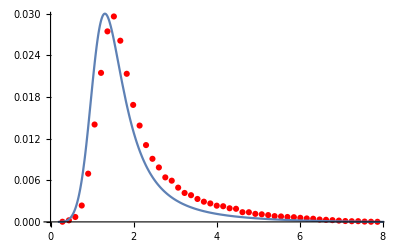

```mathematica
br = NIntegrate[100/gammaTot Ngamma[out,"W"]/.{rhoL[_]->0,rhoT[_]->Const3π*Fq3π},{q2, (3*$mPi)^2,q2Max[out]}];
brNPI[out, 3]=br;
Print["Br(3π)=",br," %"];
root = readROOT["../c++/results/"<>out<>"_3pi_q2.txt",Norm->br];
Show[
PlotHST[1.1root],
Plot[100/gammaTot Ngamma[out,"W"]/.{rhoL[_]->0,rhoT[_]->Const3π*Fq3π},{q2, (3*$mPi)^2,q2Max[out]}]
]
```

Br(5π)=0.00378203 %

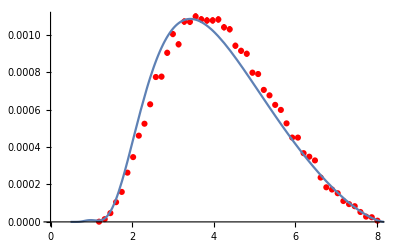

```mathematica
br = NIntegrate[100/gammaTot Ngamma[out,"W"]/.{rhoL[_]->0,rhoT[_]->Const5π*Fq5π/.{mπ->$mPi}},{q2, (5*$mPi)^2,q2Max[out]}];
brNPI[out, 5]=br;
Print["Br(5π)=",br," %"];
root = readROOT["../c++/results/"<>out<>"_5pi_q2.txt",Norm->br];
Show[
PlotHST[root],
Plot[100/gammaTot Ngamma[out,"W"]/.{rhoL[_]->0,rhoT[_]->Const5π*Fq5π/.{mπ->$mPi}},{q2, (5*$mPi)^2,q2Max[out]}]
]
```

### chi_c1

```mathematica
out="chi_c1"
```

chi_c1

Br(2π)=0.0185221 %

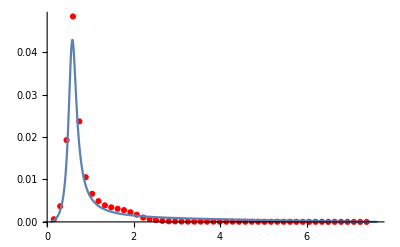

```mathematica
br = NIntegrate[100/gammaTot Ngamma[out,"W"]/.{rhoL[_]->0,rhoT[_]->Const2π*Fq2π},{q2, (2*$mPi)^2,q2Max[out]}];
brNPI[out, 2]=br;
Print["Br(2π)=",br," %"];
root = readROOT["../c++/results/"<>out<>"_2pi_q2.txt",Norm->br];
Show[
PlotHST[1.1root],
Plot[100/gammaTot Ngamma[out,"W"]/.{rhoL[_]->0,rhoT[_]->Const2π*Fq2π},{q2, (2*$mPi)^2,q2Max[out]}, PlotRange->All]
,PlotRange->All]
```

Br(3π)=0.0229855 %

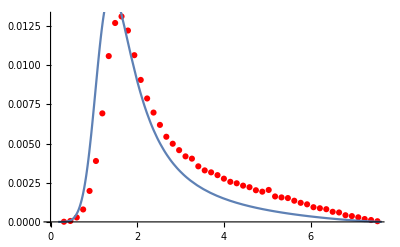

```mathematica
br = NIntegrate[100/gammaTot Ngamma[out,"W"]/.{rhoL[_]->0,rhoT[_]->Const3π*Fq3π},{q2, (3*$mPi)^2,q2Max[out]}];
brNPI[out, 3]=br;
Print["Br(3π)=",br," %"];
root = readROOT["../c++/results/"<>out<>"_3pi_q2.txt",Norm->br];
Show[
PlotHST[1.1root],
Plot[100/gammaTot Ngamma[out,"W"]/.{rhoL[_]->0,rhoT[_]->Const3π*Fq3π},{q2, (3*$mPi)^2,q2Max[out]}]
]
```

Br(5π)=0.00462799 %

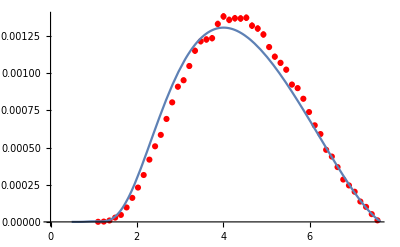

```mathematica
br = NIntegrate[100/gammaTot Ngamma[out,"W"]/.{rhoL[_]->0,rhoT[_]->Const5π*Fq5π/.{mπ->$mPi}},{q2, (5*$mPi)^2,q2Max[out]}];
brNPI[out, 5]=br;
Print["Br(5π)=",br," %"];
root = readROOT["../c++/results/"<>out<>"_5pi_q2.txt",Norm->br];
Show[
PlotHST[root],
Plot[100/gammaTot Ngamma[out,"W"]/.{rhoL[_]->0,rhoT[_]->Const5π*Fq5π/.{mπ->$mPi}},{q2, (5*$mPi)^2,q2Max[out]}]
]
```

### chi_c1

```mathematica
out="chi_c2"
```

chi_c2

Br(2π)=0.108223 %

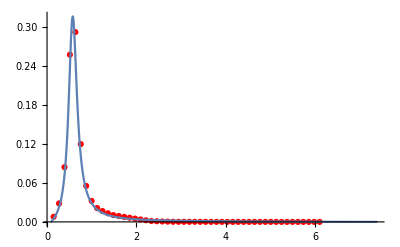

```mathematica
br = NIntegrate[100/gammaTot Ngamma[out,"W"]/.{rhoL[_]->0,rhoT[_]->Const2π*Fq2π},{q2, (2*$mPi)^2,q2Max[out]}];
brNPI[out, 2]=br;
Print["Br(2π)=",br," %"];
root = readROOT["../c++/results/"<>out<>"_2pi_q2.txt",Norm->br];
Show[
PlotHST[1.1root],
Plot[100/gammaTot Ngamma[out,"W"]/.{rhoL[_]->0,rhoT[_]->Const2π*Fq2π},{q2, (2*$mPi)^2,q2Max[out]}, PlotRange->All]
,PlotRange->All]
```

Br(3π)=0.068821 %

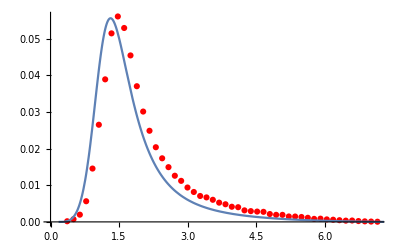

```mathematica
br = NIntegrate[100/gammaTot Ngamma[out,"W"]/.{rhoL[_]->0,rhoT[_]->Const3π*Fq3π},{q2, (3*$mPi)^2,q2Max[out]}];
brNPI[out, 3]=br;
Print["Br(3π)=",br," %"];
root = readROOT["../c++/results/"<>out<>"_3pi_q2.txt",Norm->br];
Show[
PlotHST[1.1root],
Plot[100/gammaTot Ngamma[out,"W"]/.{rhoL[_]->0,rhoT[_]->Const3π*Fq3π},{q2, (3*$mPi)^2,q2Max[out]}]
]
```

Br(5π)=0.00656311 %

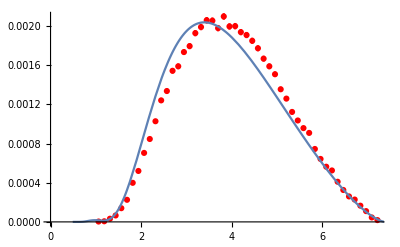

```mathematica
br = NIntegrate[100/gammaTot Ngamma[out,"W"]/.{rhoL[_]->0,rhoT[_]->Const5π*Fq5π/.{mπ->$mPi}},{q2, (5*$mPi)^2,q2Max[out]}];
brNPI[out, 5]=br;
Print["Br(5π)=",br," %"];
root = readROOT["../c++/results/"<>out<>"_5pi_q2.txt",Norm->br];
Show[
PlotHST[root],
Plot[100/gammaTot Ngamma[out,"W"]/.{rhoL[_]->0,rhoT[_]->Const5π*Fq5π/.{mπ->$mPi}},{q2, (5*$mPi)^2,q2Max[out]}]
]
```

### combined plots

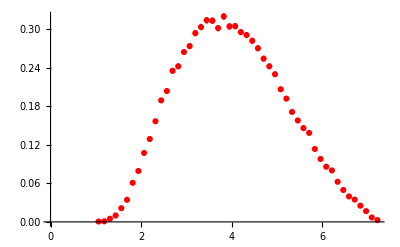

```mathematica
PlotHST[readROOT["../c++/results/"<>out<>"_5pi_q2.txt", Norm->1]]
```

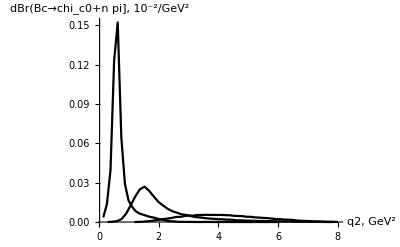

```mathematica
out = "chi_c0";
plot[2] = PlotHST[readROOT["../c++/results/"<>out<>"_2pi_q2.txt",Norm->brNPI[out, 2]], Joined->True, PlotStyle->Black, PlotRange->All, ShowErrors->False];
plot[3] = PlotHST[readROOT["../c++/results/"<>out<>"_3pi_q2.txt",Norm->brNPI[out, 3]], Joined->True, PlotStyle->Black, PlotRange->All, ShowErrors->False];
plot[5] = PlotHST[5*readROOT["../c++/results/"<>out<>"_5pi_q2.txt",Norm->brNPI[out, 5]], Joined->True, PlotStyle->Black, PlotRange->All, ShowErrors->False];
Show[{plot[2], plot[3], plot[5]}, PlotRange->All, AxesLabel->{"q2, GeV^2", "dBr(Bc→"<>out<>"+n pi], 10^-2/GeV^2"}]
```

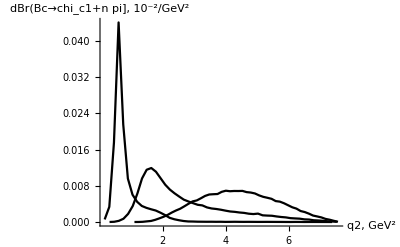

```mathematica
out = "chi_c1";
plot[2] = PlotHST[readROOT["../c++/results/"<>out<>"_2pi_q2.txt",Norm->brNPI[out, 2]], Joined->True, PlotStyle->Black, PlotRange->All, ShowErrors->False];
plot[3] = PlotHST[readROOT["../c++/results/"<>out<>"_3pi_q2.txt",Norm->brNPI[out, 3]], Joined->True, PlotStyle->Black, PlotRange->All, ShowErrors->False];
plot[5] = PlotHST[5*readROOT["../c++/results/"<>out<>"_5pi_q2.txt",Norm->brNPI[out, 5]], Joined->True, PlotStyle->Black, PlotRange->All, ShowErrors->False];
Show[{plot[2], plot[3], plot[5]}, PlotRange->All, AxesLabel->{"q2, GeV^2", "dBr(Bc→"<>out<>"+n pi], 10^-2/GeV^2"}]
```

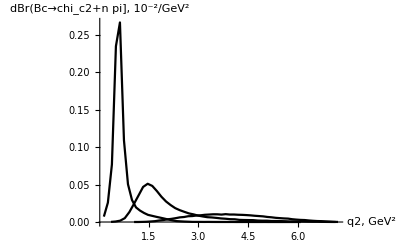

```mathematica
out = "chi_c2";
plot[2] = PlotHST[readROOT["../c++/results/"<>out<>"_2pi_q2.txt",Norm->brNPI[out, 2]], Joined->True, PlotStyle->Black, PlotRange->All, ShowErrors->False];
plot[3] = PlotHST[readROOT["../c++/results/"<>out<>"_3pi_q2.txt",Norm->brNPI[out, 3]], Joined->True, PlotStyle->Black, PlotRange->All, ShowErrors->False];
plot[5] = PlotHST[5*readROOT["../c++/results/"<>out<>"_5pi_q2.txt",Norm->brNPI[out, 5]], Joined->True, PlotStyle->Black, PlotRange->All, ShowErrors->False];
Show[{plot[2], plot[3], plot[5]}, PlotRange->All, AxesLabel->{"q2, GeV^2", "dBr(Bc→"<>out<>"+n pi], 10^-2/GeV^2"}]
```

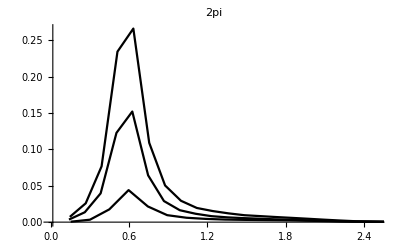

```mathematica
Show[
Table[
PlotHST[readROOT["../c++/results/"<>out<>"_2pi_q2.txt",Norm->brNPI[out, 2]], Joined->True, PlotStyle->Black, PlotRange->All, ShowErrors->False]
,{out, chiList}]
,PlotRange->{{0,2.5},All}, PlotLabel->"2pi"]
```

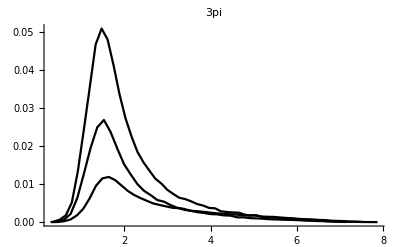

```mathematica
Show[
Table[
PlotHST[readROOT["../c++/results/"<>out<>"_3pi_q2.txt",Norm->brNPI[out, 3]], Joined->True, PlotStyle->Black, PlotRange->All, ShowErrors->False]
,{out, chiList}]
,PlotRange->{All,All}, PlotLabel->"3pi"]
```

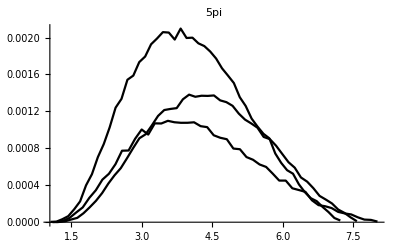

```mathematica
Show[
Table[
PlotHST[readROOT["../c++/results/"<>out<>"_5pi_q2.txt",Norm->brNPI[out, 5]], Joined->True, PlotStyle->Black, PlotRange->All, ShowErrors->False]
,{out, chiList}]
,PlotRange->{All,All}, PlotLabel->"5pi"]
```